```mathematica
Expand[Integrate[ j,{j,1,n}]]
```

-1/2+n^2/2

```mathematica
Expand[Integrate[1,{j,1,n},{k,1,n/j}]]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j k,{j,1,n},{k,1,n/j}]]
```

ConditionalExpression[1/4-n^2/4+1/2 n^2 Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j k l,{j,1,n},{k,1,n/j},{l,1,n/(j k )}]]
```

ConditionalExpression[-1/8+n^2/8-1/4 n^2 Log[n]+1/4 n^2 Log[n]^2,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j k l m,{j,1,n},{k,1,n/j},{l,1,n/(j k )},{m,1,n/(j k l )}]]
```

ConditionalExpression[1/16-n^2/16+1/8 n^2 Log[n]-1/8 n^2 Log[n]^2+1/12 n^2 Log[n]^3,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j k l m o,{j,1,n},{k,1,n/j},{l,1,n/(j k )},{m,1,n/(j k l )},{o,1,n/(j k l m )}]]
```

ConditionalExpression[-1/32+n^2/32-1/16 n^2 Log[n]+1/16 n^2 Log[n]^2-1/24 n^2 Log[n]^3+1/48 n^2 Log[n]^4,Re[n]≥0||n∉Reals]

```mathematica
-1/2+n^2/2
1/4-n^2/4+1/2 n^2 Log[n]
-1/8+n^2/8-1/4 n^2 Log[n]+1/4 n^2 Log[n]^2
1/16-n^2/16+1/8 n^2 Log[n]-1/8 n^2 Log[n]^2+1/12 n^2 Log[n]^3
-1/32+n^2/32-1/16 n^2 Log[n]+1/16 n^2 Log[n]^2-1/24 n^2 Log[n]^3+1/48 n^2 Log[n]^4
```

```mathematica
f[j_] := (-1)^(j+1)(1/2)^(j+1)+ Sum[ n^2 /k!(Log[n])^k (-1)^(j-k) (1/2)^(j-k+1), {k,0,j}]
```

```mathematica
f[0]
```

-1/2+n^2/2

```mathematica
f2[k_] := Expand[(-1)^(k+1)((1/2)^(k+1)-n^2/2 Sum[1 /j!(-Log[n])^j  (1/2)^(k-j), {j,0,k}])]
```

```mathematica
f2[3]
```

1/16-n^2/16+1/8 n^2 Log[n]-1/8 n^2 Log[n]^2+1/12 n^2 Log[n]^3

```mathematica
Expand[Integrate[ j^2,{j,1,n}]]
```

-1/3+n^3/3

```mathematica
Expand[Integrate[j^2 k^2,{j,1,n},{k,1,n/j}]]
```

ConditionalExpression[1/9-n^3/9+1/3 n^3 Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j^2 k^2 l^2,{j,1,n},{k,1,n/j},{l,1,n/(j k )}]]
```

ConditionalExpression[-1/27+n^3/27-1/9 n^3 Log[n]+1/6 n^3 Log[n]^2,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j^2 k^2 l^2 m^2,{j,1,n},{k,1,n/j},{l,1,n/(j k )},{m,1,n/(j k l )}]]
```

ConditionalExpression[1/81-n^3/81+1/27 n^3 Log[n]-1/18 n^3 Log[n]^2+1/18 n^3 Log[n]^3,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[j^2 k^2 l^2 m^2 o^2,{j,1,n},{k,1,n/j},{l,1,n/(j k )},{m,1,n/(j k l )},{o,1,n/(j k l m )}]]
```

$Aborted

```mathematica
-1/3+n^3/3
```

```mathematica
1/9-n^3/9+1/3 n^3 Log[n]
```

```mathematica
-1/27+n^3/27-1/9 n^3 Log[n]+1/6 n^3 Log[n]^2
```

```mathematica
1/81-n^3/81+1/27 n^3 Log[n]-1/18 n^3 Log[n]^2+1/18 n^3 Log[n]^3
```

```mathematica
f3[k_] := Expand[(-1)^(k+1)((1/3)^(k+1)-n^3/3 Sum[1 /j!(-Log[n])^j  (1/3)^(k-j), {j,0,k}])]
```

```mathematica
f3[3]
```

1/81-n^3/81+1/27 n^3 Log[n]-1/18 n^3 Log[n]^2+1/18 n^3 Log[n]^3

```mathematica
fs[n_,k_,s_] := Expand[(-1)^(k+1)((1/(1-s))^(k+1)-n^(1-s)/(1-s) Sum[1 /j!(-Log[n])^j  (1/(1-s))^(k-j), {j,0,k}])]
```

```mathematica
fs[n,3,0]
```

1-n+n Log[n]-1/2 n Log[n]^2+1/6 n Log[n]^3

```mathematica
ps[n_,s_]:= Sum[ (-1)^(k+1)/k N[fs[n,k,s]],{k,1,100}]
```

```mathematica
fs[n,4,ZetaZero[1]]
```

-1/(1-ZetaZero[1])^5+n^(1-ZetaZero[1])/(1-ZetaZero[1])^5-(n^(1-ZetaZero[1]) Log[n])/(1-ZetaZero[1])^4+(n^(1-ZetaZero[1]) Log[n]^2)/(2 (1-ZetaZero[1])^3)-(n^(1-ZetaZero[1]) Log[n]^3)/(6 (1-ZetaZero[1])^2)+(n^(1-ZetaZero[1]) Log[n]^4)/(24 (1-ZetaZero[1]))

```mathematica
ee[n_]:=(-0.0049864938890432945+0.00035322521742155925 ⅈ)+(0.0049864938890432945-0.00035322521742155925 ⅈ) n^(0.5-14.134725141734695 ⅈ)+(0.0024994944168615697+0.07065933315127745 ⅈ) n^(0.5-14.134725141734695 ⅈ) Log[n]
```

```mathematica
ps[100,0]
```

182.601

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

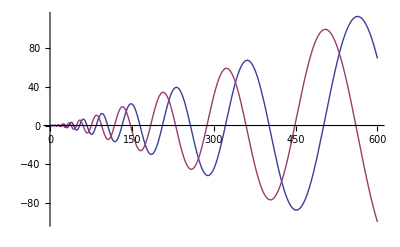

```mathematica
Plot[{Re[fs[n,cc=4,dc=1/2+14.134725141734695 I]],Im[fs[n,cc,dc]]},{n,1,600}]
```

```mathematica
fs[n,4,0]
```

-1+n-n Log[n]+1/2 n Log[n]^2-1/6 n Log[n]^3+1/24 n Log[n]^4

```mathematica
fs[n,3,0]
```

1-n+n Log[n]-1/2 n Log[n]^2+1/6 n Log[n]^3

```mathematica
N[fs[100,3,0]]
```

928.88

```mathematica
N[Gamma[4,0,-Log[100]]/Gamma[4]]
```

928.88-3.40898×10^-13 ⅈ

```mathematica
N[Integrate[t^(4-1)E^(-t),{t,0,-Log[100]}]/Gamma[4]]
```

928.88

```mathematica
fs[n,3,-1]
```

1/16-n^2/16+1/8 n^2 Log[n]-1/8 n^2 Log[n]^2+1/12 n^2 Log[n]^3

```mathematica
N[fs[100,3,-1]]
```

60009.2

```mathematica
N[Integrate[t^(4-1)E^(-2t),{t,0,-Log[100]}]/Gamma[4]]
```

60009.2

```mathematica
N[fs[100,3,-2]]
```

4.40583×10^6

```mathematica
N[Integrate[t^(4-1)E^(-3t),{t,0,-Log[100]}]/Gamma[4]]
```

4.40583×10^6

```mathematica
Integrate[t^(a-1)E^(-t),{t,0,-Log[n]}]/Gamma[a]
```

ConditionalExpression[(Gamma[a]-Gamma[a,-Log[n]])/Gamma[a],Re[a]>0]

```mathematica
Integrate[t^(a-1)E^(-2t),{t,0,-Log[n]}]/Gamma[a]
```

ConditionalExpression[(2^-a (Gamma[a]-Gamma[a,-2 Log[n]]))/Gamma[a],Re[a]>0]

```mathematica
Integrate[t^(a-1)E^(-3t),{t,0,-Log[n]}]/Gamma[a]
```

ConditionalExpression[(3^-a (Gamma[a]-Gamma[a,-3 Log[n]]))/Gamma[a],Re[a]>0]

```mathematica
Integrate[t^(a-1)E^(1t),{t,0,-Log[n]}]/Gamma[a]
```

ConditionalExpression[((Gamma[a]-Gamma[a,Log[n]]) (-Log[n])^a Log[n]^-a)/Gamma[a],Re[a]>0]

```mathematica
Integrate[t^(a-1)E^(-s t),{t,0,-Log[n]}]/Gamma[a]
```

ConditionalExpression[((Gamma[a]-Gamma[a,-s Log[n]]) (-Log[n])^a (-s Log[n])^-a)/Gamma[a],Re[a]>0]

```mathematica
(-Log[n])^a (-s Log[n])^-a/.s->-2+I
```

(-Log[n])^a ((2-ⅈ) Log[n])^-a

```mathematica
-N[Integrate[t^(2-1)E^(2 t),{t,0,-Log[100]}]]
```

-0.249745

```mathematica
Expand[((Gamma[a]-Gamma[a,-s Log[n]]) (-Log[n])^a (-s Log[n])^-a)/Gamma[a]]
```

```mathematica
Fa1[n_,a_,s_]:=(-Log[n])^a (-(1-s) Log[n])^-a-(Gamma[a,-(1-s) Log[n]] (-Log[n])^a (-(1-s) Log[n])^-a)/Gamma[a]
```

```mathematica
Fa2[n_,a_,s_]:=((Gamma[a]-Gamma[a,-(1-s) Log[n]]) (-Log[n])^a (-(1-s) Log[n])^-a)/Gamma[a]
```

```mathematica
Fa3[n_,a_,s_]:=((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
```

```mathematica
N[{Fa1[a0=140,a1=2,a2=0],Fa2[a0,a1,a2],Fa3[a0,a1,a2]}]
```

{552.83-6.75797×10^-14 ⅈ,552.83-6.75797×10^-14 ⅈ,552.83-6.75797×10^-14 ⅈ}

```mathematica
FullSimplify[((Gamma[a,0,-s Log[n]]) (-Log[n])^a (-s Log[n])^-a)/Gamma[a]]
```

```mathematica
(Gamma[a,0,-s Log[n]] (-Log[n])^a (-s Log[n])^-a)/Gamma[a]/.s->0
```

(0^-a Gamma[a,0,0] (-Log[n])^a)/Gamma[a]

```mathematica
FullSimplify[(-Log[n])^a (-s Log[n])^-a]
```

```mathematica
e1[n_,a_,s_]:=(-Log[n])^a (-s Log[n])^-a
```

```mathematica
e1[23,2,3]
```

1/9

```mathematica
e2[n_,a_,s_]:=(-Log[n])^a /(-s Log[n])^a
```

```mathematica
e2[23,2,3]
```

1/9

```mathematica
e3[n_,a_,s_]:=((Log[n]) /(s Log[n]))^a
```

```mathematica
e3[23,2,3]
```

1/9

```mathematica
e4[n_,a_,s_]:=s^-a
```

```mathematica
e4[23,2,3]
```

1/9

```mathematica
Sum[ t^(j-1)/(j!),{j,1,Infinity}]
```

(-1+ⅇ^t)/t